```mathematica
Force[z_,R1_,X1_,X2_]:=(4 R1^(1/2))/(3(X1+X2))z^(3/2)
Pot[z_,R1_,X1_,X2_]:=(8 √R1 z^(5/2))/(15 (X1+X2))
```

```mathematica
Integrate[Force[z,R1,X1,X2],z]
```

(8 √R1 z^(5/2))/(15 (X1+X2))

```mathematica
Integrate[Force[z,0.15,(1-0.4^2)/10^8,(1-0.25^2)/(1*10^9)],{z,0,0.01}]
```

221.215

```mathematica
Force[0.01,0.15,(1-0.4^2)/10^8,(1-0.25^2)/(1*10^9)]
```

55303.6

```mathematica
7*9.81*0.5
```

34.335

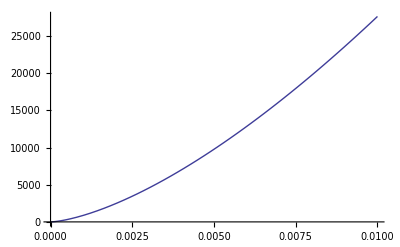

```mathematica
Plot[Force[z,0.15,(1-0.4^2)/(0.5*10^8),(1-0.25^2)/(5*10^8)],{z,0,0.01}]
```

```mathematica
20000
```

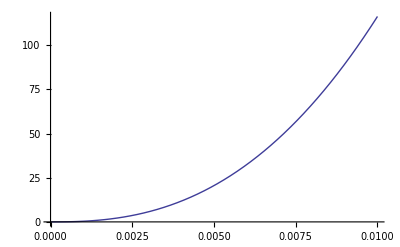

```mathematica
Plot[Pot[z,0.15,(1-0.4^2)/10^8,(1-0.25^2)/(1*10^8)],{z,0,0.01}]
```

```mathematica
hhertz[M1_,U1_,R1_,X1_,X2_]:=(15*M1*U1^2(X1+X2)/(16 R1^(1/2)))^(2/5)
```

```mathematica
hhertz[7,1,0.15,(1-0.4^2)/(0.5*10^8),(1-0.25^2)/(5*10^8)
```

0.0045889

0.013506